## Covid19 and Lockdowns in Europe.

Did Lockdowns have an effect on the death rate of Covid19 in European countries? I will conduct an enquiry into this question. I will use data analysis tools such as linear and generalized linear models to conclude various facts around this question. I will use various data sets in this enquiry, these will be “Epidemic Data for Novel Coronavirus COVID-19”,  “Coronavirus COVID-19 Pandemic Government Measures”, “COVID-19 situation update for the EU/EEA, as of 27 April 2022”, “Data on country response measures to COVID-19” and “Patient Medical Data for Novel Coronavirus COVID-19”. These data sets have been made available on the Wolfram Repository and on the European Centre for Disease Prevention and Control website. Please place them into your desktop to run the notebook. (~/Desktop/filename.csv)

```mathematica
covidData = ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];
govMeasures = ResourceData[ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]];
```

## Covid19 Deaths in Europe.

First I will have a quick look at the data. I want to enquire about the deaths caused by Covid19 in Europe, so I will have a look at the most up to date number of deaths per country in the Wolfram data set. The latest date for death rates is 30/1/2022.

First I’ll locate the European countries within the dataset. The Wolfram Repository thankfully has in build data of European countries.

```mathematica
euCovidData = Select[covidData,MemberQ[CountryData["Europe"], #[["Country"]]]&];
```

Now here is a plot of the deaths caused by Covid19 per country in Europe on  30/1/2022. This is the most up to date date of this data when writing this essay.

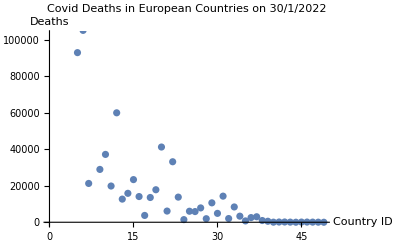

```mathematica
ListPlot[Table[Normal[euCovidData[[i]][[-1]]][[-1]][[2]], {i, 1, Length[euCovidData]}],PlotLabel->"Covid Deaths in European Countries on 30/1/2022", AxesLabel->{"Country ID", "Deaths"}]
```

Some of these values look suspiciously low. Are there any death rates that are at 0 in this data?

```mathematica
Select[Table[Normal[euCovidData[[i]][[-1]]][[-1]][[2]], {i, 1, Length[euCovidData]}], # ==0&] //Length
```

1

I’ll delete this 0 value and plot the deaths per 100, 000  people on 30/1/2022 for each European country . Using deaths per 100,000 people is a way to compare numbers between countries and is used by WHO to compare mortality rates of Covid.

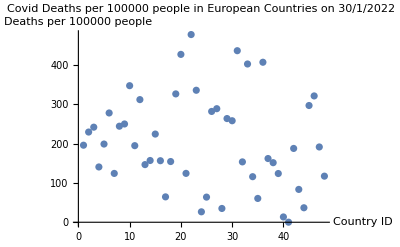

```mathematica
ListPlot[Select[Table[(Normal[Select[covidData,MemberQ[CountryData["Europe"], #[["Country"]]]&][[i]][[-1]]][[-1]][[2]] / QuantityMagnitude[Normal[Select[covidData,MemberQ[CountryData["Europe"], #[["Country"]]]&]][[i]]["Country"]["Population"]])*100000,{i, 1, Length[euCovidData]}], # >0&], PlotLabel->"Covid Deaths per 100000 people in European Countries on 30/1/2022", AxesLabel->{"Country ID", "Deaths per 100000 people"}]
```

I feel sceptical about this data as there was a zero value in it. I want to check the values with another data set to see if any other values may be incorrect. The European Centre for Disease Prevention and Control have data available on their website.

```mathematica
ecdpDeaths = Import["~/Desktop/data.csv"][[2;;, All]];
```

Next I will convert the dates column from type string to type date object.

```mathematica
ecdpDeaths[[All, 1]] = FromDateString[ecdpDeaths[[All, 1]] ,{"Day", "Month", "Year"}];
```

Now as the wolfram deaths are last recorded on 30/1/2022 I will find and select the closest available date in the ECDP data and also omit any entries with a value of 0.

```mathematica
ecdpDeaths = GroupBy[Dataset[Select[Select[ecdpDeaths, #[[1]] < DateObject[{2022, 1, 31}]&][[All, {1, 6, 7}]], #[[2]]>0&]][All,<|"date"->1,"deaths"->2, "country"->3|>], "country"];
```

Now I will calculate the total amount of deaths per country for each country and enter them into a list.

```mathematica
ecdpDeathUntilJan302022 = SortBy[Table[{Total[ecdpDeaths[[i]][[All, "deaths"]]], Interpreter["Country"][ecdpDeaths[[i]][[All, "country"]][[1]]]}, {i, 1, Length[ecdpDeaths]}], Last];
```

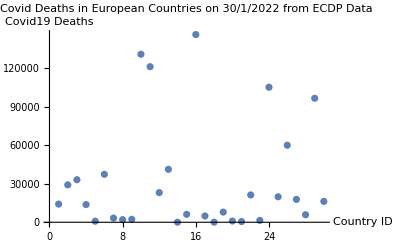

```mathematica
ListPlot[ecdpDeathUntilJan302022[[All, 1]], PlotLabel->"Covid Deaths in European Countries on 30/1/2022 from ECDP Data", AxesLabel->{"Country ID", "Covid19 Deaths"}]
```

Now I have total Covid19 deaths up until 30th Jan 2022 from 2 data sets I will compare them.

Here I select the countries (along with their deaths on 30th Jan 2022) from the wolfram data that are also in the ECDP data.

```mathematica
wolframDeathsInEcdpData = Select[euCovidData, MemberQ[Intersection[euCovidData[[All, 2]], ecdpDeathUntilJan302022[[All, 2]]], #[[2]]]&];
```

```mathematica
wolframDeathsInEcdpData = Table[{Normal[wolframDeathsInEcdpData[[i]][[-1]]][[-1]][[-1]], wolframDeathsInEcdpData[[i]][["Country"]]},{i, 1, Length[wolframDeathsInEcdpData]}];
```

I plot these two data sets alongside each other, organising both in alphabetical order, so each country occupies the same location on the x axis.

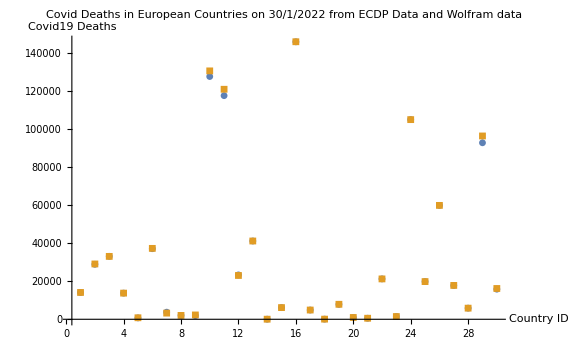

```mathematica
ListPlot[{SortBy[wolframDeathsInEcdpData, Last][[All, 1]], ecdpDeathUntilJan302022[[All, 1]]}, Filling->{1->{2}}, PlotRange->All, PlotLabel->"Covid Deaths in European Countries on 30/1/2022 from ECDP Data and Wolfram data", AxesLabel->{"Country ID", "Covid19 Deaths"}, PlotMarkers->{Automatic, Small}, ImageSize->Large]
```

They look pretty similar. Lets plot the differences. Again sorting the wolfram data into alphabetical order so the countries match the ECDP data on the x axis.

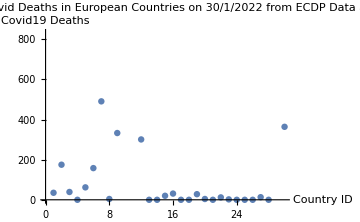

```mathematica
ListPlot[Table[Abs[SortBy[wolframDeathsInEcdpData, Last][[All, 1]][[i]] - ecdpDeathUntilJan302022[[All, 1]][[i]]], {i, 1, Length[wolframDeathsInEcdpData]}],  ImageSize->Medium, PlotLabel->"Difference between Covid Deaths in European Countries on 30/1/2022 from ECDP Data and Wolfram data", AxesLabel->{"Country ID", "Covid19 Deaths"}]
```

## Covid19 Lockdowns in Europe.

I have investigated the amount of deaths per European country so now I want to look at the Government measures employed by each European country. For this I will use the “Coronavirus COVID-19 Pandemic Government Measures” data available from the Wolfram Repository.

```mathematica
govMeasures = ResourceData[ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]];
```

Here we can see the categorise that the wolfram data is split into. I am interested in countries that have implemented a Lockdown.

```mathematica
govResCat =Table[{Normal[DeleteDuplicates[govMeasures[[All, "Category"]]]][[i]],Select[govMeasures, #[["Category"]] ==Normal[DeleteDuplicates[govMeasures[[All, "Category"]]]][[i]]&]//Length}, {i, 1, 5}];
```

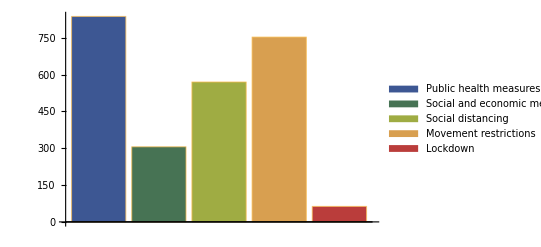

```mathematica
BarChart[govResCat[[All, 2]], ChartLegends->govResCat[[All, 1]], ChartStyle->"DarkRainbow"]
```

I will make two lists, one of the countries that had a lockdown and one of the countries that didn’t.

```mathematica
wolframLockdowns = Select[Keys[Normal[Select[GroupBy[govMeasures, "Country"], MemberQ[Normal[#[[All, "Category"]]], "Lockdown"]&]]], MemberQ[CountryData["Europe"], #]&];
```

```mathematica
wolframNoLockdowns = Select[Keys[Normal[Select[GroupBy[govMeasures, "Country"], Not[MemberQ[Normal[#[[All, "Category"]]], "Lockdown"]]&]]], MemberQ[CountryData["Europe"], #]&];
```

Here is a plot of the European countries that did not and did not have a lockdown. The Countries that did appear in blue.

```mathematica
GeoListPlot[{wolframNoLockdowns, wolframLockdowns}]
```

-Graphics-

Now I want to look at the ECPD data to check the reliability of the Wolfram data and double check if these countries did or did not have a lockdown. On their website the ECDP states that this data includes ‘stay-at-home’ orders for the general population as a category and that this is also known as a lockdown. So lets see what countries had a stay at home order or lockdown according to this data.

```mathematica
ecdpGovMeasures = Import["~/Desktop/response_graphs_data_2022-04-21.csv"];
```

```mathematica
ecdpLockdowns = Interpreter["Country"]/@DeleteDuplicates[Select[ecdpGovMeasures[[2;;, All]], #[[2]] =="StayHomeOrder"&][[All, 1]]];
```

```mathematica
ecdpNoLockdown =Interpreter["Country"]/@Select[DeleteDuplicates[ecdpGovMeasures[[2;;, 1]]], Not[MemberQ[ecdpLockdowns, Interpreter["Country"][#]]]&];
```

So which countries had a lockdown according to both of the data sets? I’ll use the Intersection function to select the countries that appeared in both of the datasets.

```mathematica
euLockdowns = Intersection[ecdpLockdowns, wolframLockdowns];
```

```mathematica
euNoLockdown = Intersection[ecdpNoLockdown, wolframNoLockdowns];
```

Here we can see that same information as the chart above but according to both of the data sets.

```mathematica
GeoListPlot[{euNoLockdown, euLockdowns}]
```

-Graphics-

Here is a plot that clearly shows that there were a lot of countries that were labelled as having a lockdown in the wolfram data but not in the ECPD data. The darker color countries were in both data sets while the light were in the wolfram but not in the ECPD data.

```mathematica
GeoListPlot[{{Join[{euNoLockdown, euLockdowns}], Join[{wolframLockdowns, wolframNoLockdowns}]}}]
```

-Graphics-

I want to work with the lists of countries that appear in both data sets as having a lockdown as therefore am more confident that that is then in fact accurate.

## Death rate per 100,000 people for European city’s with and without Lockdowns.

To be able to compare death rates per country it is important to compare deaths per 100,000 as the World Health Organisation do.

Here I will calculate the deaths per 100,000 people for each country within the lists above.

```mathematica
euLockdownsDeathsCountry = Table[{N[Normal[Select[covidData, MemberQ[euLockdowns,#["Country"]]&][[i]]["Deaths"]][[-1]][[2]]/QuantityMagnitude[Select[covidData, MemberQ[euLockdowns,#["Country"]]&][[i]]["Country"]["Population"]]*100000],Select[covidData, MemberQ[euLockdowns,#["Country"]]&][[i]]["Country"] }, {i, 1, Length[euLockdowns]}];
```

```mathematica
euNoLockdownDeathsCountry = Table[{N[Normal[Select[covidData, MemberQ[euNoLockdown,#["Country"]]&][[i]]["Deaths"]][[-1]][[2]]/QuantityMagnitude[Select[covidData, MemberQ[euNoLockdown,#["Country"]]&][[i]]["Country"]["Population"]]*100000],Select[covidData, MemberQ[euNoLockdown,#["Country"]]&][[i]]["Country"] }, {i, 1, Length[euNoLockdown]}];
```

Here is the death rates per 100,000 people for each European country that had a lockdown and beside is the countries that did not have a lockdown.

```mathematica
GraphicsRow[{GeoRegionValuePlot[euLockdownsDeathsCountry[[All, 2]]->euLockdownsDeathsCountry[[All, 1]]], GeoRegionValuePlot[euNoLockdownDeathsCountry[[All, 2]]->euNoLockdownDeathsCountry[[All, 1]]]}]
```

-Graphics-

It is interesting to note that the countries within eastern Europe appear to have higher death rates.

## Comparing countries death rates with and without Lockdowns.

First I’ll create a dataset combining the countries that did and didn’t have Lockdowns. I’ll also add True or False to show whether they did or did not have a lockdown.

```mathematica
data = Dataset[Join[Map[Append[#, True]&,euLockdownsDeathsCountry], Map[Append[#, False]&,euNoLockdownDeathsCountry]]][All, <|"deaths"->1,"country"->2,"lockdown"->3|>];
```

There are 10 countries in the lockdown group.

```mathematica
GroupBy[data, "lockdown"][[1]]//Length
```

10

There are 13 countries in the no lockdown group.

```mathematica
GroupBy[data, "lockdown"][[2]]//Length
```

13

Here is a plot of these deaths per 100,000 people.

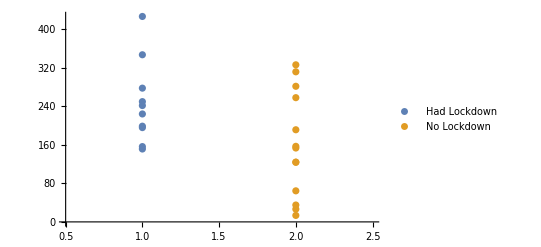

```mathematica
ListPlot[{Map[Append[#, 1]&,euLockdownsDeathsCountry][[All, {3, 1}]], Map[Append[#, 2]&,euNoLockdownDeathsCountry][[All, {3, 1}]]}, PlotRange->{{0.5, 2.5}, All}, Ticks->{None,Automatic}, PlotLegends->{"Had Lockdown", "No Lockdown"}]
```

What is the mean values of the two groups?

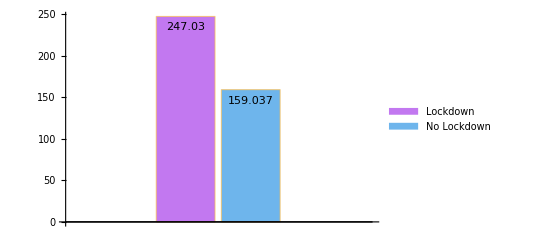

```mathematica
BarChart[{GroupBy[data, "lockdown"][[1]][[All, 1]]//Mean, GroupBy[data, "lockdown"][[2]][[All, 1]]//Mean}, ChartStyle->"Pastel", ChartLegends->{"Lockdown", "No Lockdown"}, LabelingFunction->Top, PlotRange->All]
```

## ANOVA Analysis

Now I can answer the question - is there a correlation between countries that had a lockdown and their death rates per 100,000 people of Covid19 on 30/1/2022.

First, I will prep the data so it is in a form I can make a linear model with.

```mathematica
data = Transpose[{Normal[data[[All, 1]]], Normal[data[[All, 3]]]}][[All, {2, 1}]];
```

Now I will fit a linear model.

```mathematica
lm1 = LinearModelFit[data, {1, x}, x, NominalVariables->x]
```

FittedModel[247.03-87.9925 DiscreteIndicator[x,False,{False,True}]]

Here is the parameter table. We can see both of the variables with the model are statistically significant as both have a p-value less than 0.05.

```mathematica
lm1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 247.03 | 31.5406 | 7.83213 | 1.15504×10^-7
x[False] | -87.9925 | 41.9529 | -2.09741 | 0.0482397

The r squared value for this model is small, which is not good.

```mathematica
lm1["RSquared"]
```

0.1732

```mathematica
StandardDeviation[lm1["FitResiduals"]]
```

97.4469

```mathematica
lm1["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 43763. | 43763. | 4.39914 | 0.0482397
Error | 21 | 208910. | 9948.08 |  | 
Total | 22 | 252673. |  |  |

Now I will fit another model but setting the countries that did not have a lockdown as the baseline.

```mathematica
lm1b = LinearModelFit[data/.{True ->"zTrue"}, {1, x}, x, NominalVariables->x]
```

FittedModel[159.037+87.9925 DiscreteIndicator[x,zTrue,{zTrue,False}]]

```mathematica
lm1b["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 159.037 | 27.6629 | 5.74912 | 0.0000104687
x[zTrue] | 87.9925 | 41.9529 | 2.09741 | 0.0482397

The countries with a lockdown had an average of 159 deaths per 100,000 people on 30/1/2022 while the countries without a lockdown had an average of 247 deaths per 100,000 people on 30/1/2022 — a difference of 88 which was statistically significant (F_(1,21)=4.3; p=0.048).

From the above analysis we can see the death rate of the countries which had a lockdown was significantly greater than that of the countries without a lockdown. (F_(1,21)=4.39; p=0.048)

This is a surprising outcome, I would have expected the countries with a lockdown to have a lower death rate, but it  is not what is shown here.

## A closer look at a lockdown.

Austria had a lockdown within the dates of 26th December 2020 and 7th February 2021.

That is shown in the ECDP data here.

```mathematica
govMesECDP = Import["~/Desktop/response_graphs_data_2022-04-21.csv"];
```

```mathematica
Select[govMesECDP[[2;;, All]], #[[2]] =="StayHomeOrder"&][[3]]
```

{Austria,StayHomeOrder,2020-12-26,2021-02-07}

To look at this data closer I will first select the Austrian data from the data.

```mathematica
austriaData =Select[ecdpDeaths, #[[3, 3]]=="Austria"&][[1]];
```

Now I will select the data within the date range of 26th December 2020 and 7th February 2021.

```mathematica
austriaData = Select[austriaData, #[[1]]<DateObject["2021-02-07"]&&#[[1]]>DateObject["2020-12-26"]&];
```

To plot this data accurately I will create a time series from it. I will extract the dates and deaths both into lists and then transpose them together into a list of lists.

```mathematica
austriaDataTS = Transpose[{austriaData[[All,1]]//Normal, austriaData[[All, 2]]//Normal}];
```

Now to plot this time series within a date list plot.

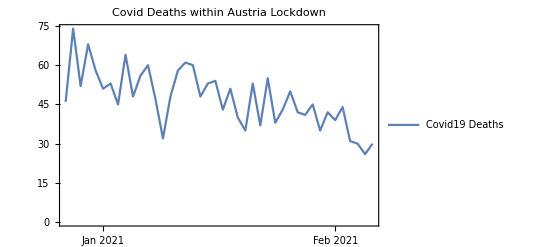

```mathematica
DateListPlot[austriaDataTS, PlotLegends->{"Covid19 Deaths"}, PlotLabel->"Covid Deaths within Austria Lockdown"]
```

I will fit a linear model to test whether this lockdown was successful in reducing the death rate in Austria . First I will get a list of the deaths per day in chronological order. I will fit a straight line as this will be adequate in judging whether the downwards trend in the data is statistically significant.

```mathematica
austriaLockdownDeaths = SortBy[austriaDataTS, First][[All, 2]];
```

```mathematica
lm = LinearModelFit[austriaLockdownDeaths, {x, 1}, x]
```

FittedModel[60.5296-0.615995 x]

Now I will plot the model along with the original data points and the mean prediction bands at a 40%.

```mathematica
bands[x_]=lm["MeanPredictionBands", ConfidenceLevel->.40];
```

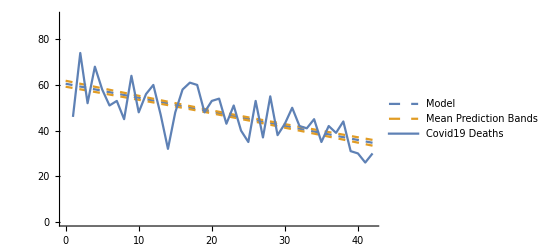

```mathematica
Show[Plot[{lm["BestFit"],bands[x]},{x, 0, Length[austriaLockdownDeaths]}, PlotLegends->{{"Model", "Mean Prediction Bands"}},  PlotStyle->Dashed], ListLinePlot[austriaLockdownDeaths, PlotLegends->{"Covid19 Deaths"}], PlotRange->{All, {0, 90}}, AxesOrigin->0]
```

Here is the R Squared of the model.

```mathematica
lm["RSquared"]
```

0.48571

As it is closer to 0 than 1, it indicated the model could be better.

So the model could be better based on the RSquared but are the fit residuals normally distrusted and uncorrelated?

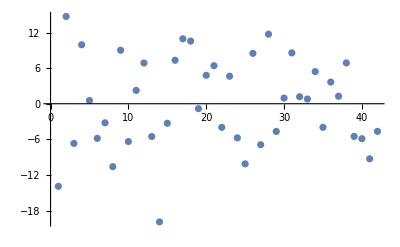

```mathematica
ListPlot[lm["FitResiduals"]]
```

I’ll use find distribution to get a rough idea if they are normally distributed.

```mathematica
FindDistribution[lm["FitResiduals"]]
```

NormalDistribution[-0.118257,8.38146]

It appears so. I' ll make a hypothesis test to be more confident in this .

```mathematica
hpyTest = DistributionFitTest[lm["FitResiduals"], NormalDistribution[-0.11825695574986335,8.381463940730429], "HypothesisTestData"]["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[-0.118257,8.38146] is not rejected at the 5 percent level based on the Cramér-von Mises test.

From the above distribution fit test we can conclude that the fit residuals of the model are normally distributed . This supports the idea that the model is a good fit.

Now I will have a look at the correlation of the fit residuals .

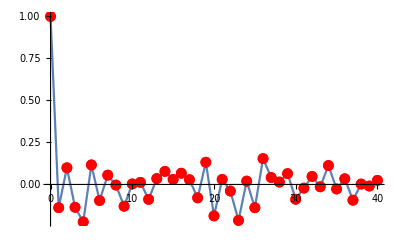

```mathematica
Transpose[{Range[0, 40],CorrelationFunction[lm["FitResiduals"],{40}]}]//ListLinePlot[#, Mesh->Full, MeshStyle->Red, PlotRange->All]&
```

To understand if these fit residuals are uncorrelated, I will repeatedly randomize their order and plot the results, as I know this will be uncorrelated .

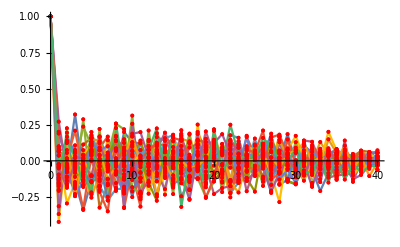

```mathematica
Table[Transpose[{Range[0, 40],CorrelationFunction[RandomSample[lm["FitResiduals"]],{40}]}],{30}]//ListLinePlot[#, Mesh->Full, MeshStyle->Red, PlotRange->All]&
```

Now I can see that the original fit residuals are very likely to be uncorrelated as their values fall between the observed range of where they would be when I know they are uncorrelated .

There is a negative co efficient within the model, I will look at the parameter table to see if this co efficient is statistically significant .

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | -0.615995 | 0.100222 | -6.14631 | 2.94315×10^-7
1 | 60.5296 | 2.47361 | 24.4702 | 1.11074×10^-25

The negative co efficient of the model is highly statistically significant with a p value of 2.94315×10^-7 . This proves that the deaths per day due to Covid19 decreased within the dates of 26th December 2020 and 7th February 2021, which were the months that a lockdown was imposed . This supports the hypothesis that lookdowns effectively decrease the daily death rate of Covid19.

## Why is there a correlation between countries that did have a lockdown and higher death rates per 100,000 population?

The result of the previous analysis feels counter intuitive. Could the populations age be a factor at play here? I will create a generalized linear model to test the hypothesis that age is a significant factor in Covid19 death rates of hospital admissions. I will use China’s data that is available from the wolfram repository.

First I will import the data, grouping it by country and selecting the first index, which is china.

```mathematica
hosData = GroupBy[ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"][[All, {1, 5, 21}]], "Country"][[1]];
```

Global`DateInterval::shdw: Symbol DateInterval appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Now I will select all the rows that have integers in the first column as not every row does.

```mathematica
hosData = Select[hosData, IntegerQ[#[[1]]]&];
```

Now I will make a list of lists containing the age of the hospital admission and a 0 or 1 which represents whether they died or not. 1 represents those who died and 0 represents those that lived.

```mathematica
died = Normal[Select[hosData, #[[-1]]==True&][[All, 1]]];
```

```mathematica
died = Table[{died[[i]], 1}, {i, 1, Length[died]}];
```

```mathematica
lived = Normal[Select[hosData, Head[#[[-1]]] == Missing&][[All, 1]]];
```

```mathematica
lived = Table[{lived[[i]], 0}, {i, 1, Length[lived]}];
```

```mathematica
data = Join[died, lived];
```

Now I will create a generalized linear model which treats the 1’s and 0’s as a nominal variable and that will calculate the probability of death given an age from the data from the Chinese hospital admissions.

```mathematica
glmChina = GeneralizedLinearModelFit[data, {age}, {age}, ExponentialFamily->"Binomial"];
```

Here is a plot of the age against the probability of death.

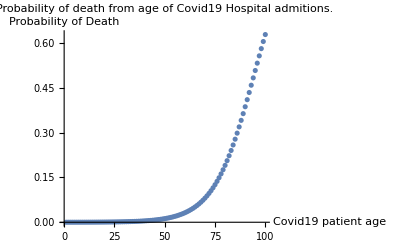

```mathematica
ListPlot[Table[glmChina[x], {x, 1, 100 }], PlotLabel->"Probability of death from age of Covid19 Hospital admitions.", AxesLabel->{ "Covid19 patient age", "Probability of Death"}]
```

We can see that there is an upward trend in the likelihood of death as age increases.

```mathematica
glmChina["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.33106 | 0.835074 | -11.1739 | 5.47054×10^-29
age | 0.0985358 | 0.0120507 | 8.17675 | 2.91597×10^-16

The age was found to be statistically significant with a P value of 2.91597×10^-16. This shows that the age of a patient who is admitted to hospital with Covid19 has an effect on the likely hood they will die or not.

Now that age has been established as a significant factor in the probability of death from Covid19, I will look at whether the countries that had a high death rate per 100,000 also had a high population age.

First I will set the data variable name to the Europe lockdown data.

```mathematica
data = Dataset[Join[Map[Append[#, True]&,euLockdownsDeathsCountry], Map[Append[#, False]&,euNoLockdownDeathsCountry]]][All, <|"deaths"->1,"country"->2,"lockdown"->3|>];
```

Now I will add the mean age of that country to the dataset.

```mathematica
data = data[All,Append[#,"medianAge"->#country["MedianAge"]]&];
```

I will plot the mean age of the country against the cases per 100,000 people.

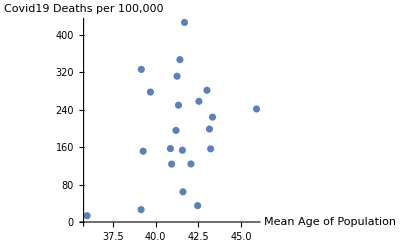

```mathematica
ListPlot[data[[All, {4, 1}]], AxesLabel->{"Mean Age of Population", "Covid19 Deaths per 100,000"}]
```

There does not  seem to be an increase of death rate with an increase of the populations median age .

I will create a linear model to fit a straight line to this data to test this. I will omit the last entry as the median age is not available.

```mathematica
lmData =Transpose[{QuantityMagnitude/@Normal[data[[All, {4, 1}]]][[All, 1]], Normal[data[[All, {4, 1}]]][[All, 2]]}][[;;-2]];
```

```mathematica
lm = LinearModelFit[lmData, {1, x}, x]
```

FittedModel[-441.895+15.4447 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -441.895 | 489.979 | -0.901864 | 0.377862
x | 15.4447 | 11.8214 | 1.30651 | 0.206205

We can see that the median age of the population is not a statistically significant factor on the countries death rate per 100,00 as neither parameter in the model has a p-value of below 0.05.

So does the population density have an impact?

I’ll add this to the dataset.

```mathematica
dataPopDen = data[All,Append[#,"populationDensity"->QuantityMagnitude[#country["PopulationDensity"]]]&];
```

```mathematica
lmData =Transpose[{Normal[dataPopDen[[All, {4, 1}]]][[All, 1]]//QuantityMagnitude, Normal[dataPopDen[[All, {4, 1}]]][[All, 2]]}];
```

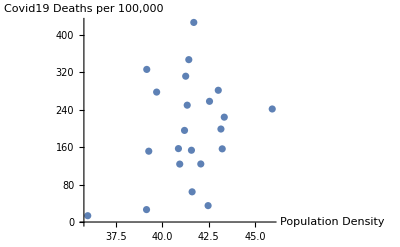

```mathematica
ListPlot[lmData, AxesLabel->{"Population Density", "Covid19 Deaths per 100,000"}]
```

```mathematica
lm = LinearModelFit[Select[lmData,Head[#[[1]]]==Real&], {1,x}, x]
```

FittedModel[-441.895+15.4447 x]

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 19866.6 | 19866.6 | 1.70697 | 0.206205
Error | 20 | 232770. | 11638.5 |  | 
Total | 21 | 252637. |  |  |

We can see from this that the negative coefficient is not statistically significant (F_(1,20)=1.70697; p=0.206)which shows that there is not a correlation between the death rate of a country and it’s population density.

## Deaths per 100,000 population and age-specific mortality rate.

It was shown above that the European countries that did have a lockdown were actually correlated with higher deaths per 100, 000 population . Why would governments decide to implement lockdowns if this was the case . It was also shown that age is a statistically significant  factor in a patients probability in dying from Covid19 . Perhaps the correct way to test if lockdowns’ have a correlation with reduced death rates is to compare the age-standardized mortality rate . The World Health Organization explains this can be an appropriate way to compare deaths . ‘Measuring how many people die each year and why they have died is one of the most  informative ways of assessing the  effectiveness of a country' s health system . Mortality data allow health authorities to evaluate how they prioritize public health programs .   Deaths can be represented as a total number per year, or as a rate per 100 000 population per year . The numbers of deaths per 100 000 population are influenced by the age distribution of the population . Two populations with the same age - specific mortality rates for a particular cause of death will have different overall death rates if the age distributions of their populations are different . Age - standardized mortality rates may be used to compare mortality in a country with a younger population to mortality in a country with an older population .  They adjust for differences in the age distribution of the population by applying the observed age - specific mortality rates for each population to a standard population .   The numbers of deaths per 100 000 population are influenced by the age distribution of the population . Two populations with the same age - specific mortality rates for a particular cause of death will have different overall death rates if the age distributions of their populations are different . Age - standardized mortality rates adjust for differences in the age distribution of the population by applying the observed age - specific mortality rates for each population to a standard population.’

I'll look at the patient data available on the Wolfram Repository, taking the European countries .

```mathematica
euHosData = Select[GroupBy[ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"][[All, {1, 5, 21}]], "Country"], MemberQ[CountryData["Europe"], #[[1, 2]]]&];
```

And plot the length of the columns for each country.

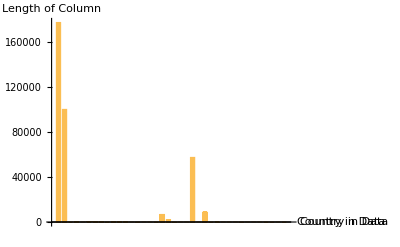

```mathematica
BarChart[Table[euHosData[[i]]//Length, {i, 1, Length[euHosData]}], AxesLabel->{"Country in Data", "Length of Column"}]
```

Here we can see that the data that includes the age of the patient in the European countries is greatly lacking . So the question of whether there is a correlation between the European countries that did implement a lockdown and their age - specific mortality rate from Covid19 cannot be answered as there is insufficient data for a meaningful answer.